# Automatic Generator of Amplitudes in the vacuum model.

## Definition of the matrix elements of the Bianchi I constraint operator

```mathematica
The definition here corresponds to Theta_{v2,v1}.  v1 is the second element.
```

```mathematica
OffD[v1_,v2_,m1_,m2_]:=a^2/b
Diag[v1_,m1_,m2_]:=b-2 a^2/b
```

## Definition of the parameters of the expansion

```mathematica
δ;
```

## Functions Used In Evaluating Amplitudes

```mathematica
Amp generates the amplitude corresponding to a generic discrete history.
Changes and paths together generate the set of all possible paths between the initial and final volume with m transitions.
ManyAmp them takes that set of paths and computes the overall amplitude.
```

```mathematica
Nume[v_]:=(ⅈ (-1)^(Length[v]-1))/(2π)Product[OffD[v[[i]],v[[i+1]],m1,m2],{i,1,Length[v]-1}];
Denompos[v_]:=Product[(Diag[v[[i]],m1,m2]+ⅈ δ),{i,1,Length[v]}];
Denomneg[v_]:=Product[(Diag[v[[i]],m1,m2]-ⅈ δ),{i,1,Length[v]}];
Amp[v_]:=Nume[v](1/Denompos[v]-1/Denomneg[v]);
Changes[m_,vi_,vf_]:=(
diff=(vf-vi)/4;
base=Join[Table[4,{i,1,m/2+diff/2}],Table[-4,{i,1,m/2-diff/2}]];
changes=Permutations[base];
numpaths=Length[changes];)
Paths[m_,vi_,vf_]:=(
paths=Table[1,{j,1,numpaths}];
path=Table[vi,{i,1,m+1}];
For[j=1,j≤numpaths,j++,
For[i=1,i≤m,i++,
path[[i+1]]=path[[i]]+changes[[j]][[i]];];
paths[[j]]=path;
];);
NullPath[v_]:=Product[v[[i]],{i,1,Length[v]}];
ManyAmp[m_,vi_,vf_]:=(
Changes[m,vi,vf];
Paths[m,vi,vf];
Many=0;
For[i=1,i≤Length[paths],i++,
Many=Many+Amp[paths[[i]]];
];
Many)
```

```mathematica
ManyAmp[8,4,4]
Many
```

(35 ⅈ a^8 (-1/(b-ⅈ δ)^9+1/(b+ⅈ δ)^9))/π

```mathematica
Clear[a,b,δ]
Sum[ⅈ/(2π)(a^(2m)/(b+ⅈ δ)^(2m+1)-a^(2m)/(b-ⅈ δ)^(2m+1))Binomial[2m,m],{m,0,∞}]
```

(ⅈ (b √(1-(4 a^2)/(b-ⅈ δ)^2)-b √(1-(4 a^2)/(b+ⅈ δ)^2)-ⅈ √(1-(4 a^2)/(b-ⅈ δ)^2) δ-ⅈ √(1-(4 a^2)/(b+ⅈ δ)^2) δ))/(2 π √(1-(4 a^2)/(b-ⅈ δ)^2) √(1-(4 a^2)/(b+ⅈ δ)^2) (b-ⅈ δ) (b+ⅈ δ))

```mathematica
Exact[a_,b_,δ_]:=(ⅈ (b √(1-(4 a^2)/(b-ⅈ δ)^2)-b √(1-(4 a^2)/(b+ⅈ δ)^2)-ⅈ √(1-(4 a^2)/(b-ⅈ δ)^2) δ-ⅈ √(1-(4 a^2)/(b+ⅈ δ)^2) δ))/(2 π √(1-(4 a^2)/(b-ⅈ δ)^2) √(1-(4 a^2)/(b+ⅈ δ)^2) (b-ⅈ δ) (b+ⅈ δ));
```

1

0.5

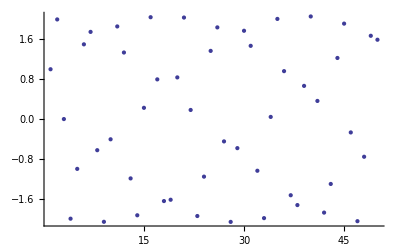

```mathematica
a=1
b=.5
psi=Table[1,{i,1,50}];
psi[[1]]=1;
psi[[2]]=2;
For[n=3,n≤50,n++,
	psi[[n]]=-psi[[n-2]]+b/a psi[[n-1]]]
ListPlot[psi]
```

```mathematica
ManyAmp[0,4,4]
```

(ⅈ (-1/(0.1-ⅈ δ)+1/(0.1+ⅈ δ)))/(2 π)

0.01

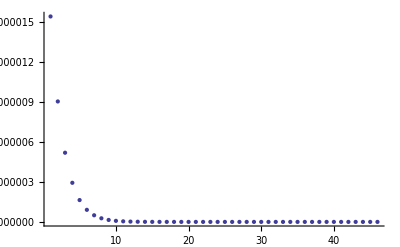

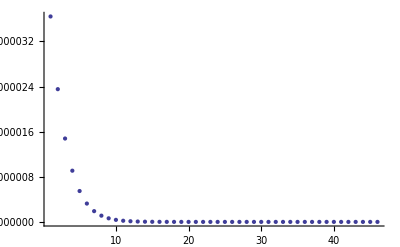

```mathematica
δ=0.01
m0=Table[ManyAmp[n,4,4+4n],{n,5,50}];
m1=Table[ManyAmp[n+2,4,4+4n],{n,5,50}];
ListPlot[Re[m0]]
ListPlot[Re[m1]]
```